```mathematica
(* output = response ** input
goal = preemph ** response ** input 
preemphLT = goalLT/responseLT/inputLT
```

```mathematica
input=HeavisideTheta[t];
output=HeavisideTheta[t]*(1-a0 Exp[-t/τ0]);
goal=HeavisideTheta[t]*(1-a1 Exp[-t/τ1]);
responseLT=LaplaceTransform[output,t,s]/LaplaceTransform[input,t,s]
goalLT=LaplaceTransform[goal,t,s]/LaplaceTransform[input,t,s]
```

s (1/s-(a0 τ0)/(1+s τ0))

s (1/s-(a1 τ1)/(1+s τ1))

```mathematica
preemphLT=goalLT/responseLT
```

(1/s-(a1 τ1)/(1+s τ1))/(1/s-(a0 τ0)/(1+s τ0))

```mathematica
preemph=FullSimplify[InverseLaplaceTransform[preemphLT,s,t]]/.DiracDelta[t]->0
```

((a1 ⅇ^(-t/τ1) (-τ0+τ1))/τ1-(a0 ⅇ^(t/((-1+a0) τ0)) ((-1+a0) τ0+τ1-a1 τ1))/((-1+a0)^2 τ0))/((-1+a0) τ0+τ1)

```mathematica
preemph/.{a0->0.95,a1->0.95}
```

(-(380. ⅇ^(-(20. t)/τ0) (-0.05 τ0+0.05 τ1))/τ0+(0.95 ⅇ^(-t/τ1) (-τ0+τ1))/τ1)/(-0.05 τ0+τ1)

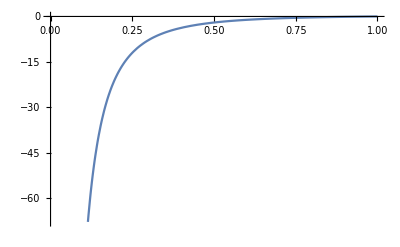

```mathematica
Plot[preemph/.{τ0->1,t->0},{τ1,0,1}]
```

```mathematica
response=InverseLaplaceTransform[responseLT,s,t]
```

(a0 ⅇ^(-t/τ0))/τ0+DiracDelta[t]-a0 DiracDelta[t]

1-(ⅇ^(-t/τpre) (-apre τ0+a0 apre τ0+apre τpre))/(τ0-τpre)-(ⅇ^(-t/τ0) (a0 τ0-a0 τpre-a0 apre τpre))/(τ0-τpre)

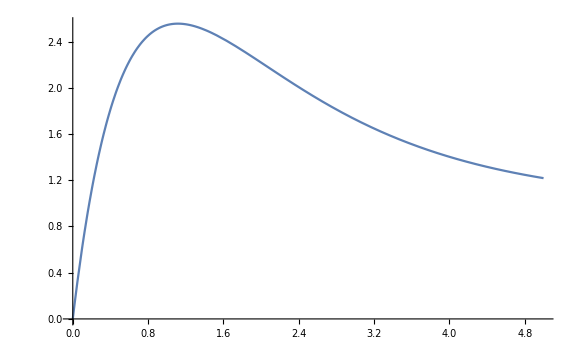

```mathematica
inputwpre=HeavisideTheta[t](1+apre*Exp[-t/τpre]);
inputwpreLT=LaplaceTransform[inputwpre,t,s];
outputwpreLT=inputwpreLT*responseLT;
outputwpre=InverseLaplaceTransform[outputwpreLT,s,t]
Plot[outputwpre/.{a0->1,τ0->1.6,τpre->0.6,apre->10},{t,0,5},ImageSize->Large]
```